```mathematica
quit[]
(* Variable declarations *)
mt=0.18;(*kg*)
mw=0.1;(*kg*)
la=0.35;(*cm*)
lw=0.28;(*cm*)
lh=0.2475;(*cm*)
kf=0.61029972;(*N/V*)
mf = 0.09;(*kg*)
(* Setting UP matrices *)
A = {{0, 1, 0 ,0},{0,0,0,0},{0,0,0,1},{0,0,0,0}};
MatrixForm[A]
```

quit[]

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
B = {{0,0},{(kf*lh)/(2*mf*lh*lh), (-kf*lh)/(2*mf*lh*lh)}, {0,0}, {(kf*la)/((mt*la*la)+(mw*lw*lw)), (kf*la)/((mt*la*la)+(mw*lw*lw))}};
MatrixForm[B]
```

(0 | 0
13.6992 | -13.6992
0 | 0
7.14637 | 7.14637)

```mathematica
Cm = {{1,0,0,0},{0,0,1,0}};
MatrixForm[Cm]
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
Dm = {{0,0},{0,0}};
MatrixForm[Dm]
```

(0 | 0
0 | 0)

```mathematica
(*Obtaining the eigenvalues and vector*)
Eigenvalues[A]
```

{0,0,0,0}

```mathematica
Eigenvectors[A]
```

{{0,0,1,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*We have 4 repeated eigenvalues*)
(*Plotting to see the response of the system for a step input, Uf = Ub = 1* and assuming that we were initially at equilibrium, therefore X0 = {0,0,-40deg,0}*)
Utemp = {1,1};
U = Transpose[Utemp];
MatrixForm[U]
```

(1
1)

```mathematica
X0 = Transpose[{0,0,(320*Pi)/180, 0}];
MatrixForm[X0]
```

(0
0
(16 π)/9
0)

```mathematica
Xs[t] = MatrixExp [t A].X0 + ∫_0^t MatrixExp[(t - τ)A].B.U ⅆτ//Simplify//Chop;
MatrixForm[Xs[t]]
```

(0
0
5.58505+7.14637 t^2
14.2927 t)

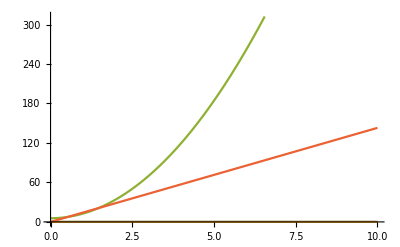

```mathematica
Plot[Evaluate[Xs[t]],{t,0,10}]
```

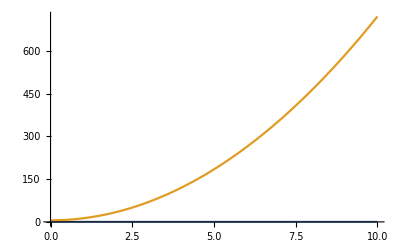

```mathematica
(*PLotting the output*)
Y[t] = Cm.Xs[t];
Plot[Evaluate[Y[t]],{t,0,10}]
```

```mathematica
(*Checking Controllability*)
```

```mathematica
A1 = A.B;
MatrixForm[A1]
A2 = A.A1;
MatrixForm[A2]
A3 = A.A2;
MatrixForm[A3]
```

(13.6992 | -13.6992
0. | 0.
7.14637 | 7.14637
0. | 0.)

(0. | 0.
0. | 0.
0. | 0.
0. | 0.)

(0. | 0.
0. | 0.
0. | 0.
0. | 0.)

```mathematica
MatrixForm[B]
```

(0 | 0
13.6992 | -13.6992
0 | 0
7.14637 | 7.14637)

```mathematica
P = Join[B, A.B, A.A.B, A.A.A.B,2];
MatrixForm[P]
```

(0 | 0 | 13.6992 | -13.6992 | 0. | 0. | 0. | 0.
13.6992 | -13.6992 | 0. | 0. | 0. | 0. | 0. | 0.
0 | 0 | 7.14637 | 7.14637 | 0. | 0. | 0. | 0.
7.14637 | 7.14637 | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
MatrixRank[P]
```

4

```mathematica
(*Since the rank of P is equal to N, then the system is controllable*)
(*Checking Observability *)
MatrixForm[Transpose[Cm]]
A4 = Transpose[A] . Transpose[Cm];
MatrixForm[A4]
A5 = Transpose[A.A]. Transpose[Cm];
MatrixForm[A5]
A6 = Transpose[A.A.A]. Transpose[Cm];
MatrixForm[A6]
```

(1 | 0
0 | 0
0 | 1
0 | 0)

(0 | 0
1 | 0
0 | 0
0 | 1)

(0 | 0
0 | 0
0 | 0
0 | 0)

(0 | 0
0 | 0
0 | 0
0 | 0)

```mathematica
Q = Join[Transpose[Cm],A4,A5,A6,2];
MatrixForm[Q]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
MatrixRank[Q]
```

4

```mathematica
(*The System is fully observalbe*)
(*Attempting to design a state feedback controller using *)
MatrixForm[A]
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
K = {{K11,K12,K13,K14},{K21,K22,K23,K24}};
MatrixForm[K]
```

(K11 | K12 | K13 | K14
K21 | K22 | K23 | K24)

```mathematica
λ = {λ1,λ2,λ3,λ4};
MatrixForm[λ]
I4 = IdentityMatrix[4];
MatrixForm[I4]
```

(λ1
λ2
λ3
λ4)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
n=4;
r=2;
```

```mathematica
Xsf = Join[I4 ℒ -A,B,2]; MatrixForm[Xsf] (*Where ℒ is here temporarily until we handle λ*)
```

(ℒ | -1 | 0 | 0 | 0 | 0
0 | ℒ | 0 | 0 | 13.6992 | -13.6992
0 | 0 | ℒ | -1 | 0 | 0
0 | 0 | 0 | ℒ | 7.14637 | 7.14637)

```mathematica
υ = Transpose[NullSpace[Xsf]] //Chop;
MatrixForm[υ]
```

(13.6992/ℒ^2 | -13.6992/ℒ^2
13.6992/ℒ | -13.6992/ℒ
-7.14637/ℒ^2 | -7.14637/ℒ^2
-7.14637/ℒ | -7.14637/ℒ
0 | 1.
1. | 0)

```mathematica
Ψ = Take[υ,n];
MatrixForm[Ψ]
```

(13.6992/ℒ^2 | -13.6992/ℒ^2
13.6992/ℒ | -13.6992/ℒ
-7.14637/ℒ^2 | -7.14637/ℒ^2
-7.14637/ℒ | -7.14637/ℒ)

```mathematica
ϝ = Take[υ,-r];
MatrixForm[ϝ]
```

(0 | 1.
1. | 0)

```mathematica
(*Now this was generally how the Ψ should look, and we need to substitute λ with each value once then join that matrix. In the tut/lec, we would add the eigenvalues before getting ψ and ϝ, but doing this beforehand wont affect anything mathematically*)
(*Adding the symbolic values of λ in order to get the full correct matrix we need*)
```

```mathematica
(*λ={-12.9999,-12.9997,-12.9996,-12.9995};
Ω = Join[Ψ /. ℒ -> λ[[1]],Ψ /. ℒ -> λ[[2]],Ψ /. ℒ -> λ[[3]],Ψ /. ℒ -> λ[[4]],2];
Λ = Join[ϝ /. ℒ -> λ[[1]],ϝ /. ℒ -> λ[[2]],ϝ /. ℒ -> λ[[3]],ϝ /. ℒ -> λ[[4]],2];
columnChoice = {1,2,4,7};
G = Ω[[All,columnChoice]];
𝒥 = Λ[[All, columnChoice]];
K = 𝒥 . Inverse[G];
MatrixForm[K]
*)
```

```mathematica
(*(*Plotting to see the response again*)
An = A-B.K;
Eigenvalues[An]
F ={{1,1},{1,1}};
MatrixForm[F]
Bn = B.F;
V = Transpose[{1,1}];
Xc[t] = MatrixExp [t An].X0 + ∫_0^t MatrixExp[(t - τ)An].Bn.V ⅆτ//Simplify//Chop;
MatrixForm[Xc[t]]
Plot[Evaluate[Xc[t]],{t,0,10}]*)
```

```mathematica
(*Yc[t] = Cm.Xc[t];
Plot[Evaluate[Yc[t]],{t,0,10}]*)
```

```mathematica
min=10000000000000;
λ={-12.9999,-12.9997,-12.9996,-12.9995};
Ω = Join[Ψ /. ℒ -> λ[[1]],Ψ /. ℒ -> λ[[2]],Ψ /. ℒ -> λ[[3]],Ψ /. ℒ -> λ[[4]],2];
Λ = Join[ϝ /. ℒ -> λ[[1]],ϝ /. ℒ -> λ[[2]],ϝ /. ℒ -> λ[[3]],ϝ /. ℒ -> λ[[4]],2];
selected = {s1,s2,s3,s4};
For[i=1,i<9,i++,
For[j=1,j<9,j++,
For[o=1,o<9,o++,
For[h=1,h<9,h++,
columnChoice = {i,j,o,h};
G = Ω[[All,columnChoice]];
𝒥 = Λ[[All, columnChoice]];
If[i==j || i==o || i==h || j==o || j==h || h==o,Continue,
If[0<Abs[Det[G]]<min,selected = columnChoice; min=Det[G];Print[min],Continue]
]
]
]
]
]
Print[selected]
```

-1.88013×10^-12

{1,2,3,4}

```mathematica
G = Ω[[All,selected]];
𝒥 = Λ[[All, selected]];
K = 𝒥 . Inverse[G];
MatrixForm[K]
```

(6.16805 | 0.948945 | 11.8238 | 1.81908
-6.16805 | -0.948945 | 11.8238 | 1.81908)

{-12.9999,-12.9999,-12.9997,-12.9997}

(1 | 1
1 | 1)

(-28369.1 ⅇ^(-12.9999 t)+29915.4 ⅇ^(-12.9999 t)-30006.4 ⅇ^(-12.9997 t)+28460.1 ⅇ^(-12.9997 t)
-2.18279×10^-10+368795. ⅇ^(-12.9999 t)-388898. ⅇ^(-12.9999 t)+390075. ⅇ^(-12.9997 t)-369973. ⅇ^(-12.9997 t)
0.16915-42673.6 ⅇ^(-12.9999 t)-331240. ⅇ^(-12.9999 t)+331112. ⅇ^(-12.9997 t)+42806.6 ⅇ^(-12.9997 t)
-2.51021×10^-10+554752. ⅇ^(-12.9999 t)+4.30608×10^6 ⅇ^(-12.9999 t)-4.30436×10^6 ⅇ^(-12.9997 t)-556473. ⅇ^(-12.9997 t))

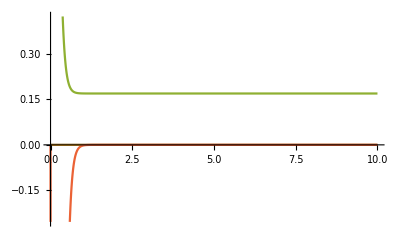

```mathematica
(*Plotting to see the response again*)
An = A-B.K;
Eigenvalues[An]
F ={{1,1},{1,1}};
MatrixForm[F]
Bn = B.F;
V = Transpose[{1,1}];
Xc[t] = MatrixExp [t An].X0 + ∫_0^t MatrixExp[(t - τ)An].Bn.V ⅆτ//Simplify//Chop;
MatrixForm[Xc[t]]
Plot[Evaluate[Xc[t]],{t,0,10}]
```

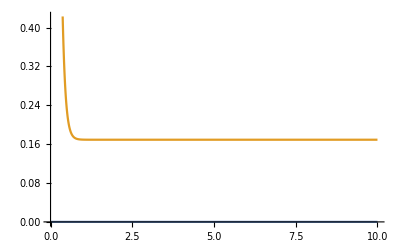

```mathematica
Yc[t] = Cm.Xc[t];
Plot[Evaluate[Yc[t]],{t,0,10}]
```